```mathematica
issues = {{1,12},{2,27},{3,32},{4,114},{5,180},{6,230},{7,272},{8,317},{9,336},{10,350},{11,394},{12,400}}
```

```mathematica
{{1,12},{2,27},{3,32},{4,114},{5,180},{6,230},{7,272},{8,317},{9,336},{10,350},{11,394},{12,400}}
```

Goel model

```mathematica
goel = NonlinearModelFit[issues, a(1 - Exp[-b*t]), {a,b},t]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
goel["BestFit"]
```

30469.7 (1-ⅇ^(-0.00116718 t))

```mathematica
goel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 30469.7 | 822719. | 0.0370354 | 0.971186
b | 0.00116718 | 0.0316877 | 0.0368337 | 0.971343

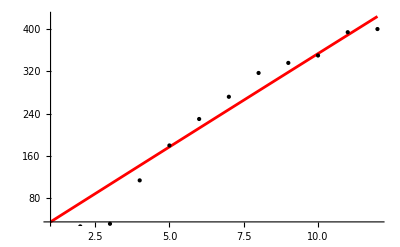

```mathematica
Plot[goel[x], {x, 1, 12}, Epilog->Point[issues], PlotRange->All, PlotStyle->Red]
```

```mathematica
dataGoel = {#, goel[#]} & [{"AIC", "AICc", "BIC", "RSquared", "AdjustedRSquared"}]
```

{{AIC,AICc,BIC,RSquared,AdjustedRSquared},{122.718,125.718,124.173,0.985735,0.982882}}

```mathematica
TableForm[dataGoel]
```

AIC | AICc | BIC | RSquared | AdjustedRSquared
122.718 | 125.718 | 124.173 | 0.985735 | 0.982882

Delayed S-shaped model m(t) = a(1-(1+b*t)Exp[-b*t])

```mathematica
delayedS = NonlinearModelFit[issues,a(1-(1+b*t)Exp[-b*t]),{{a,204}, {b,0.1}},t];
```

```mathematica
delayedS["BestFit"]
```

544.99 (1-ⅇ^(-0.228405 t) (1+0.228405 t))

```mathematica
delayedS["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 544.99 | 50.0789 | 10.8826 | 7.28343×10^-7
b | 0.228405 | 0.0234473 | 9.7412 | 2.02032×10^-6

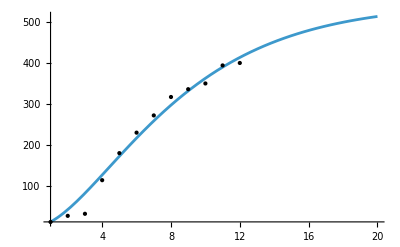

```mathematica
Plot[delayedS[x],{x,1,20},Epilog->Point[issues], PlotRange->All]
```

Inflection S-shaped model m(t) = a (1-Exp[-b*t]) / 1+ β*Exp[-b*t]

```mathematica
inflection = NonlinearModelFit[issues,(a(1-Exp[-b*t])) / (1+ β*Exp[-b*t]),{{a,204}, {b,0.1},{β}}, t];
```

```mathematica
inflection["BestFit"]
```

(396.5 (1-ⅇ^(-0.578805 t)))/(1+23.6085 ⅇ^(-0.578805 t))

```mathematica
inflection["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 396.5 | 14.5362 | 27.2768 | 5.79922×10^-10
b | 0.578805 | 0.0745775 | 7.76112 | 0.0000281774
β | 23.6085 | 9.41363 | 2.50791 | 0.0334251

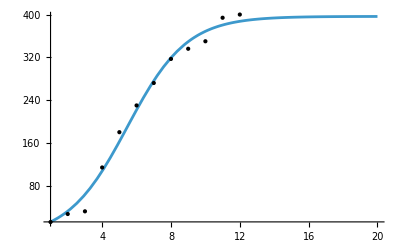

```mathematica
Plot[inflection[x],{x,1,20},Epilog->Point[issues], PlotRange->All]
```

Pham-Zhang model

```mathematica
phamZhang=NonlinearModelFit[issues,
(1/(1+β*Exp[-b*t]))*((c+a)*
(1-Exp[-b*t])-((a*b)/(b-α))*(Exp[-α*t]-Exp[-b*t])),{a,b,{c,90},{α,1.1},β},t];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
phamZhang["BestFit"]
```

(782.105 (1-ⅇ^(-1.08064 t))-729.756 (-ⅇ^(-1.08064 t)+ⅇ^(-0.054888 t)))/(1+62.0816 ⅇ^(-1.08064 t))

```mathematica
phamZhang["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 692.69 | 1040.66 | 0.665629 | 0.526966
b | 1.08064 | 0.223468 | 4.83579 | 0.00188686
c | 89.4152 | 198.126 | 0.451305 | 0.665419
α | 0.054888 | 0.157868 | 0.347684 | 0.738298
β | 62.0816 | 60.1897 | 1.03143 | 0.336652

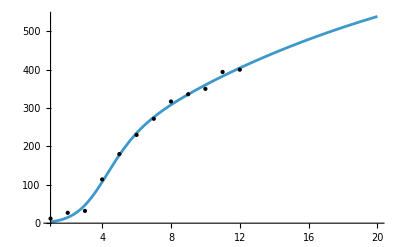

```mathematica
Plot[phamZhang[x],{x,1,20},Epilog->Point[issues], PlotRange->All]
```

PHZ model

```mathematica
phz=NonlinearModelFit[issues,
(a/(1+β *Exp[-b*t])) * 
((1-Exp[-b*t])(1-α/b)+α*a*t),
{{a,90},b,α,β},t]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[…]

```mathematica
phz["BestFit"]
```

-(107.414 (0.988351 (1-ⅇ^(0.43924 t))+0.549599 t))/(1+0.253574 ⅇ^(0.43924 t))

```mathematica
phz["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -107.414 | 138.062 | -0.778013 | 0.45895
b | -0.43924 | 0.0918732 | -4.78094 | 0.001389
α | -0.00511665 | 0.0070234 | -0.728515 | 0.487074
β | 0.253574 | 0.316891 | 0.800193 | 0.446708

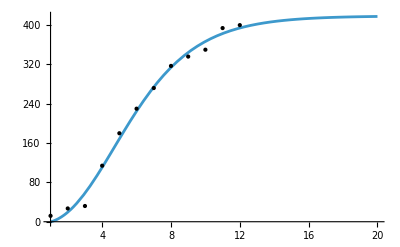

```mathematica
Plot[phz[x],{x,1,20},Epilog->Point[issues], PlotRange->All]
```